```mathematica
Music=Import["E:\\MyWorkShop\\midi\\music\\yanni\\santorin.mid"];
```

```mathematica
Music[[1]]=Sort[Music[[1]],#1[[2,1]]<#2[[2,1]]&]
```

{SoundNote[Tambourine,{0.,0.250627},SoundVolume→0.941176],SoundNote[HiHatClosed,{0.,0.125313},SoundVolume→0.941176],4129,SoundNote[E5,{95.3008,96.3072},Violin,SoundVolume→0.996078],SoundNote[E6,{95.3008,96.3072},Violin,SoundVolume→0.996078]}
 |  |  |  |

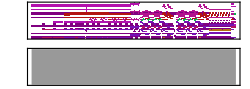

```mathematica
Sound[Music]
```

```mathematica
Try=Music[[1]];
```

```mathematica
%102
```

<|C→0,D→2,E→4,F→5,G→7,A→9,B→11|>

```mathematica
Do[
If[ToString@Head[Try[[i,3]]]≠"Rule",
Try[[i,3]]="Piano",
Try[[i,1]]],
{i,1,Length[Try]}
]
Try
```

{SoundNote[Tambourine,{0.,0.250627},SoundVolume→0.941176],SoundNote[HiHatClosed,{0.,0.125313},SoundVolume→0.941176],4129,SoundNote[E5,{95.3008,96.3072},Piano,SoundVolume→0.996078],SoundNote[E6,{95.3008,96.3072},Piano,SoundVolume→0.996078]}
 |  |  |  |

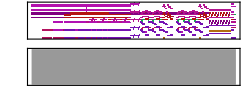

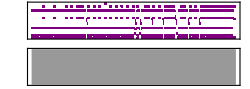

```mathematica
filtered=Select[Music[[1]],ToString[Head[#[[3]]]]!=ToString[Rule]&];
Sound[filtered]
remained=Select[Music[[1]],ToString[Head[#[[3]]]]==ToString[Rule]&];
Sound[remained]
```

```mathematica
Sort[remained,#1[[2,1]]<#2[[2,1]]&]
```

{SoundNote[SideStick,{0.,0.125313},SoundVolume→0.784314],SoundNote[BassDrum,{0.,0.125313},SoundVolume→0.784314],1342,SoundNote[MidTom2,{95.3008,96.3072},SoundVolume→0.784314],SoundNote[CrashCymbal2,{95.3008,96.3072},SoundVolume→0.784314]}
 |  |  |  |

```mathematica
filtered[[All,2]]
```

{{0.,0.250627},{0.,0.250627},{0.,0.250627},{0.,0.250627},{0.,0.250627},{0.,0.250627},2775,{95.3008,96.3072},{95.3008,96.3072},{95.3008,97.623},{95.3008,97.623},{95.3008,96.3072},{95.3008,96.3072}}
 |  |  |  |

```mathematica
Rand=RandomSample[filtered[[All,4]]];
```

```mathematica
filtered2=filtered
```

{SoundNote[G4,{0.,0.250627},Piano,SoundVolume→0.996078],SoundNote[C5,{0.,0.250627},Piano,SoundVolume→0.996078],2783,SoundNote[E5,{95.3008,96.3072},Violin,SoundVolume→0.996078],SoundNote[E6,{95.3008,96.3072},Violin,SoundVolume→0.996078]}
 |  |  |  |

```mathematica
Do[filtered2[[i,4]]=Rand[[i]],{i,1,Length[filtered]}]
```

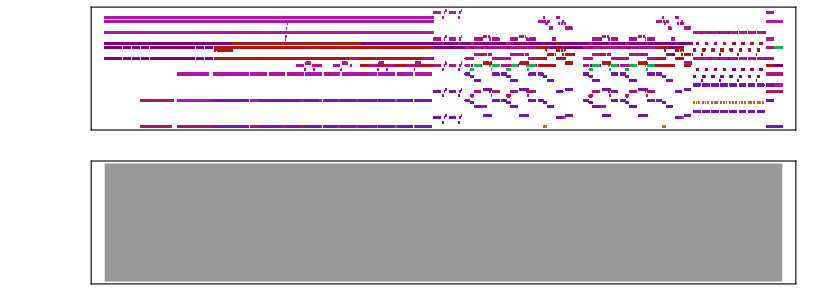

```mathematica
Sound[filtered2]
```

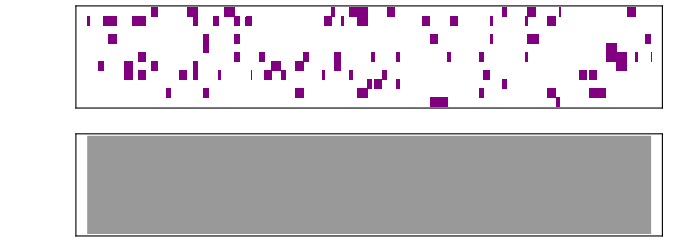

```mathematica
Sound[Table[SoundNote[NestList[#+1&,-8,n=10] (RandomChoice[{1-#,#}->{0,1}]&/@(RealDigits[N[1/7,n+1]][[1]]/50))/.x_/;x==0->None,RandomReal[{0,1}]],{i,102}]]
```

```mathematica
A={0};
shift=1;NoteNumber=100;
Do[A=Append[A,RandomInteger[{A[[i-1]]-shift,A[[i-1]]+shift}]],{i,2,NoteNumber}]
```

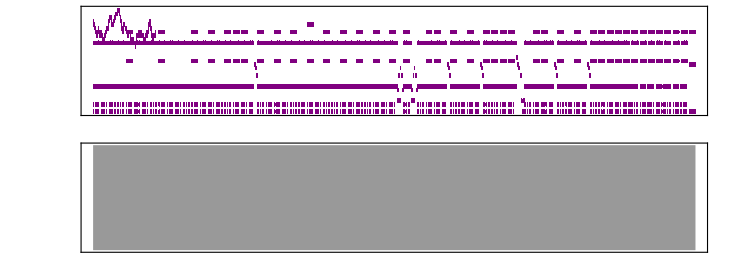

```mathematica
Sound[Table[SoundNote[A[[i]],0.1],{i,1,NoteNumber}]~Join~remained]
```

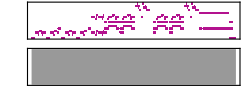

```mathematica
Sound[Select[Music[[1]],#[[3]]=="BrassSection"&]]
```

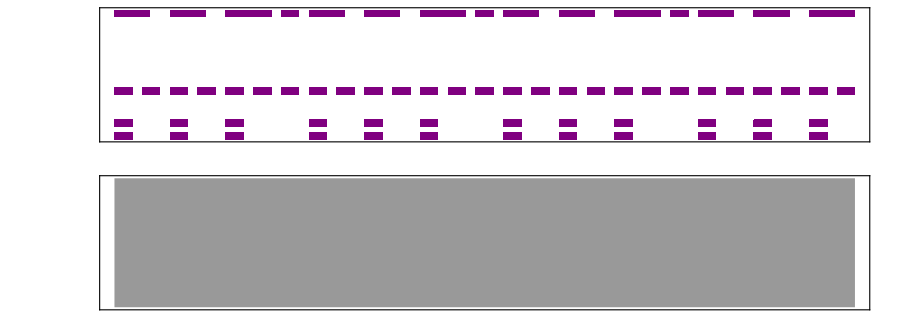

```mathematica
remained2=remained[[1;;70]];
accompany=Select[remained2,#[[1]]=="HiHatClosed"||#[[1]]=="BassDrum"||#[[1]]=="SideStick"||#[[1]]=="Tambourine"&];
Sound[accompany]
```

```mathematica
InstrumentList=DeleteDuplicates[filtered[[All,3]]~Join~remained[[All,1]]]
tonality=DeleteDuplicates[filtered[[All,3]]];
percussion=DeleteDuplicates[remained[[All,1]]];
```

{Piano,Violin,Strings,Timpani,Trombone,BassAndLead,Trumpet,Viola,BrassSection,Tambourine,HiHatClosed,BassDrum,SideStick,CrashCymbal,CrashCymbal2,MidTom2,MidTom,LowTom,RideCymbal2,LowFloorTom,Snare,HighTom}

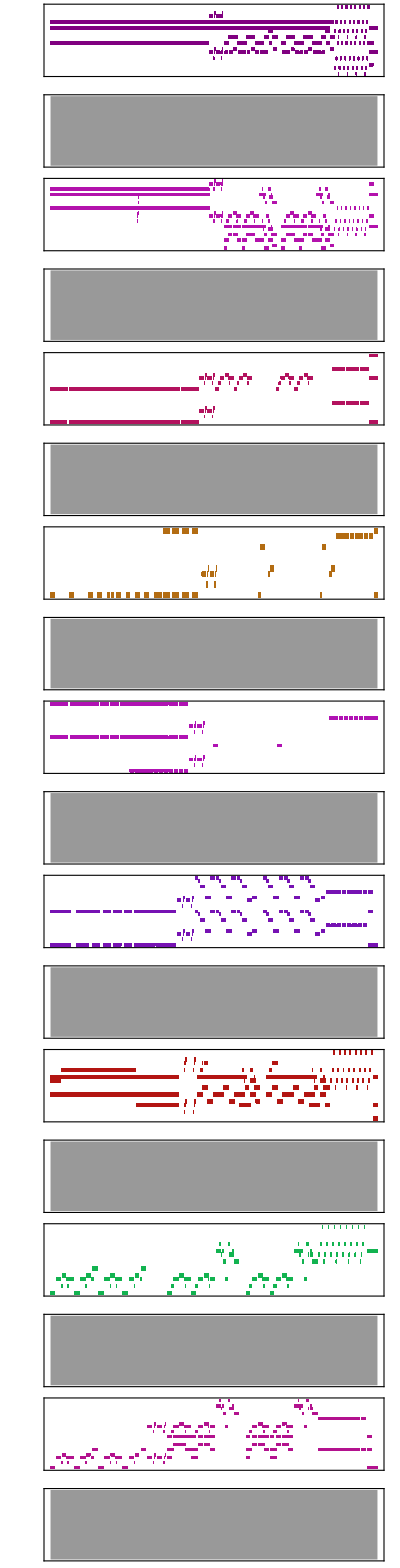

```mathematica
Column@Table[
Sound[
Select[filtered,#[[3]]==tonality[[i]]&]
],{i,1,9}]
```

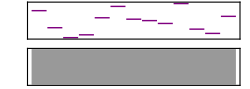

```mathematica
Sound[Table[SoundNote[InstrumentList[[i]]],{i,10,Length[InstrumentList]}]]
```

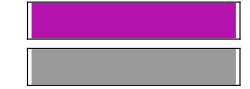

```mathematica
Sound[{SoundNote[0,1,"Violin"]}]
```

```mathematica
Sound[SoundNote[0,"BassDrum"]]
```

Sound[SoundNote[0,BassDrum]]

```mathematica
Select[filtered,#[[3]]=="Violin"&]
```

{SoundNote[G5,{0.,0.250627},Violin,SoundVolume→0.996078],SoundNote[C6,{0.,0.250627},Violin,SoundVolume→0.996078],SoundNote[D6,{0.,0.250627},Violin,SoundVolume→0.996078],SoundNote[G5,{0.37594,0.626567},Violin,SoundVolume→0.996078],SoundNote[C6,{0.37594,0.626567},Violin,SoundVolume→0.996078],SoundNote[D6,{0.37594,0.626567},Violin,SoundVolume→0.996078],SoundNote[G5,{0.75188,1.12782},Violin,SoundVolume→0.996078],SoundNote[C6,{0.75188,1.06516},Violin,SoundVolume→0.996078],SoundNote[D6,{0.75188,1.06516},Violin,SoundVolume→0.996078],SoundNote[G5,{0.75188,1.06516},Violin,SoundVolume→0.996078],SoundNote[D6,{0.93985,1.12782},Violin,SoundVolume→0.996078],SoundNote[G5,{0.93985,1.12782},Violin,SoundVolume→0.996078],SoundNote[C6,{0.93985,1.12782},Violin,SoundVolume→0.996078],SoundNote[D6,{1.12782,1.25313},Violin,SoundVolume→0.996078],SoundNote[C6,{1.12782,1.25313},Violin,SoundVolume→0.996078],SoundNote[G5,{1.12782,1.25313},Violin,SoundVolume→0.996078],SoundNote[G5,{1.31579,1.56642},Violin,SoundVolume→0.996078],SoundNote[C6,{1.31579,1.56642},Violin,SoundVolume→0.996078],SoundNote[D6,{1.31579,1.56642},Violin,SoundVolume→0.996078],SoundNote[G5,{1.69173,1.94236},Violin,SoundVolume→0.996078],SoundNote[C6,{1.69173,1.94236},Violin,SoundVolume→0.996078],SoundNote[D6,{1.69173,1.94236},Violin,SoundVolume→0.996078],SoundNote[G5,{2.06767,2.44361},Violin,SoundVolume→0.996078],SoundNote[C6,{2.06767,2.38095},Violin,SoundVolume→0.996078],SoundNote[D6,{2.06767,2.38095},Violin,SoundVolume→0.996078],SoundNote[G5,{2.06767,2.38095},Violin,SoundVolume→0.996078],SoundNote[D6,{2.25564,2.44361},Violin,SoundVolume→0.996078],SoundNote[G5,{2.25564,2.44361},Violin,SoundVolume→0.996078],SoundNote[C6,{2.25564,2.44361},Violin,SoundVolume→0.996078],SoundNote[D6,{2.44361,2.56892},Violin,SoundVolume→0.996078],SoundNote[C6,{2.44361,2.56892},Violin,SoundVolume→0.996078],SoundNote[G5,{2.44361,2.56892},Violin,SoundVolume→0.996078],SoundNote[G5,{2.63158,2.88221},Violin,SoundVolume→0.996078],SoundNote[C6,{2.63158,2.88221},Violin,SoundVolume→0.996078],SoundNote[D6,{2.63158,2.88221},Violin,SoundVolume→0.996078],SoundNote[G5,{3.00752,3.25815},Violin,SoundVolume→0.996078],SoundNote[C6,{3.00752,3.25815},Violin,SoundVolume→0.996078],SoundNote[D6,{3.00752,3.25815},Violin,SoundVolume→0.996078],SoundNote[G5,{3.38346,3.7594},Violin,SoundVolume→0.996078],SoundNote[C6,{3.38346,3.69674},Violin,SoundVolume→0.996078],SoundNote[D6,{3.38346,3.69674},Violin,SoundVolume→0.996078],SoundNote[G5,{3.38346,3.69674},Violin,SoundVolume→0.996078],SoundNote[D6,{3.57143,3.7594},Violin,SoundVolume→0.996078],SoundNote[G5,{3.57143,3.7594},Violin,SoundVolume→0.996078],SoundNote[C6,{3.57143,3.7594},Violin,SoundVolume→0.996078],SoundNote[D6,{3.7594,3.88471},Violin,SoundVolume→0.996078],SoundNote[C6,{3.7594,3.88471},Violin,SoundVolume→0.996078],SoundNote[G5,{3.7594,3.88471},Violin,SoundVolume→0.996078],SoundNote[G5,{3.94737,4.198},Violin,SoundVolume→0.996078],SoundNote[C6,{3.94737,4.198},Violin,SoundVolume→0.996078],SoundNote[D6,{3.94737,4.198},Violin,SoundVolume→0.996078],SoundNote[G5,{4.32331,4.57394},Violin,SoundVolume→0.996078],SoundNote[C6,{4.32331,4.57394},Violin,SoundVolume→0.996078],SoundNote[D6,{4.32331,4.57394},Violin,SoundVolume→0.996078],SoundNote[G5,{4.69925,5.07519},Violin,SoundVolume→0.996078],SoundNote[C6,{4.69925,5.01253},Violin,SoundVolume→0.996078],SoundNote[D6,{4.69925,5.01253},Violin,SoundVolume→0.996078],SoundNote[G5,{4.69925,5.01253},Violin,SoundVolume→0.996078],SoundNote[D6,{4.88722,5.07519},Violin,SoundVolume→0.996078],SoundNote[G5,{4.88722,5.07519},Violin,SoundVolume→0.996078],SoundNote[C6,{4.88722,5.07519},Violin,SoundVolume→0.996078],SoundNote[D6,{5.07519,5.2005},Violin,SoundVolume→0.996078],SoundNote[C6,{5.07519,5.2005},Violin,SoundVolume→0.996078],SoundNote[G5,{5.07519,5.2005},Violin,SoundVolume→0.996078],SoundNote[G5,{5.26316,5.51379},Violin,SoundVolume→0.996078],SoundNote[C6,{5.26316,5.51379},Violin,SoundVolume→0.996078],SoundNote[D6,{5.26316,5.51379},Violin,SoundVolume→0.996078],SoundNote[G5,{5.6391,5.88973},Violin,SoundVolume→0.996078],SoundNote[C6,{5.6391,5.88973},Violin,SoundVolume→0.996078],SoundNote[D6,{5.6391,5.88973},Violin,SoundVolume→0.996078],SoundNote[G5,{6.01504,6.39098},Violin,SoundVolume→0.996078],SoundNote[C6,{6.01504,6.32832},Violin,SoundVolume→0.996078],SoundNote[D6,{6.01504,6.32832},Violin,SoundVolume→0.996078],SoundNote[G5,{6.01504,6.32832},Violin,SoundVolume→0.996078],SoundNote[D6,{6.20301,6.39098},Violin,SoundVolume→0.996078],SoundNote[G5,{6.20301,6.39098},Violin,SoundVolume→0.996078],SoundNote[C6,{6.20301,6.39098},Violin,SoundVolume→0.996078],SoundNote[D6,{6.39098,6.51629},Violin,SoundVolume→0.996078],SoundNote[C6,{6.39098,6.51629},Violin,SoundVolume→0.996078],SoundNote[G5,{6.39098,6.51629},Violin,SoundVolume→0.996078],SoundNote[G5,{6.57895,6.82958},Violin,SoundVolume→0.996078],SoundNote[C6,{6.57895,6.82958},Violin,SoundVolume→0.996078],SoundNote[D6,{6.57895,6.82958},Violin,SoundVolume→0.996078],SoundNote[G5,{6.95489,7.20552},Violin,SoundVolume→0.996078],SoundNote[C6,{6.95489,7.20552},Violin,SoundVolume→0.996078],SoundNote[D6,{6.95489,7.20552},Violin,SoundVolume→0.996078],SoundNote[G5,{7.33083,7.70677},Violin,SoundVolume→0.996078],SoundNote[C6,{7.33083,7.64411},Violin,SoundVolume→0.996078],SoundNote[D6,{7.33083,7.64411},Violin,SoundVolume→0.996078],SoundNote[G5,{7.33083,7.64411},Violin,SoundVolume→0.996078],SoundNote[D6,{7.5188,7.70677},Violin,SoundVolume→0.996078],SoundNote[G5,{7.5188,7.70677},Violin,SoundVolume→0.996078],SoundNote[C6,{7.5188,7.70677},Violin,SoundVolume→0.996078],SoundNote[D6,{7.70677,7.83208},Violin,SoundVolume→0.996078],SoundNote[C6,{7.70677,7.83208},Violin,SoundVolume→0.996078],SoundNote[G5,{7.70677,7.83208},Violin,SoundVolume→0.996078],SoundNote[G5,{7.89474,8.14537},Violin,SoundVolume→0.996078],SoundNote[C6,{7.89474,8.14537},Violin,SoundVolume→0.996078],SoundNote[D6,{7.89474,8.14537},Violin,SoundVolume→0.996078],SoundNote[G5,{8.27068,8.52131},Violin,SoundVolume→0.996078],SoundNote[C6,{8.27068,8.52131},Violin,SoundVolume→0.996078],SoundNote[D6,{8.27068,8.52131},Violin,SoundVolume→0.996078],SoundNote[G5,{8.64662,9.02256},Violin,SoundVolume→0.996078],SoundNote[C6,{8.64662,8.9599},Violin,SoundVolume→0.996078],SoundNote[D6,{8.64662,8.9599},Violin,SoundVolume→0.996078],SoundNote[G5,{8.64662,8.9599},Violin,SoundVolume→0.996078],SoundNote[D6,{8.83459,9.02256},Violin,SoundVolume→0.996078],SoundNote[G5,{8.83459,9.02256},Violin,SoundVolume→0.996078],SoundNote[C6,{8.83459,9.02256},Violin,SoundVolume→0.996078],SoundNote[D6,{9.02256,9.14787},Violin,SoundVolume→0.996078],SoundNote[C6,{9.02256,9.14787},Violin,SoundVolume→0.996078],SoundNote[G5,{9.02256,9.14787},Violin,SoundVolume→0.996078],SoundNote[G5,{9.21053,9.46116},Violin,SoundVolume→0.996078],SoundNote[C6,{9.21053,9.46116},Violin,SoundVolume→0.996078],SoundNote[D6,{9.21053,9.46116},Violin,SoundVolume→0.996078],SoundNote[G5,{9.58647,9.8371},Violin,SoundVolume→0.996078],SoundNote[C6,{9.58647,9.8371},Violin,SoundVolume→0.996078],SoundNote[D6,{9.58647,9.8371},Violin,SoundVolume→0.996078],SoundNote[G5,{9.96241,10.3384},Violin,SoundVolume→0.996078],SoundNote[C6,{9.96241,10.2757},Violin,SoundVolume→0.996078],SoundNote[D6,{9.96241,10.2757},Violin,SoundVolume→0.996078],SoundNote[G5,{9.96241,10.2757},Violin,SoundVolume→0.996078],SoundNote[D6,{10.1504,10.3384},Violin,SoundVolume→0.996078],SoundNote[G5,{10.1504,10.3384},Violin,SoundVolume→0.996078],SoundNote[C6,{10.1504,10.3384},Violin,SoundVolume→0.996078],SoundNote[D6,{10.3384,10.4637},Violin,SoundVolume→0.996078],SoundNote[C6,{10.3384,10.4637},Violin,SoundVolume→0.996078],SoundNote[G5,{10.3384,10.4637},Violin,SoundVolume→0.996078],SoundNote[G5,{10.5263,10.7769},Violin,SoundVolume→0.996078],SoundNote[C6,{10.5263,10.7769},Violin,SoundVolume→0.996078],SoundNote[D6,{10.5263,10.7769},Violin,SoundVolume→0.996078],SoundNote[G5,{10.9023,11.1529},Violin,SoundVolume→0.996078],SoundNote[C6,{10.9023,11.1529},Violin,SoundVolume→0.996078],SoundNote[D6,{10.9023,11.1529},Violin,SoundVolume→0.996078],SoundNote[G5,{11.2782,11.6541},Violin,SoundVolume→0.996078],SoundNote[C6,{11.2782,11.5915},Violin,SoundVolume→0.996078],SoundNote[D6,{11.2782,11.5915},Violin,SoundVolume→0.996078],SoundNote[G5,{11.2782,11.5915},Violin,SoundVolume→0.996078],SoundNote[D6,{11.4662,11.6541},Violin,SoundVolume→0.996078],SoundNote[G5,{11.4662,11.6541},Violin,SoundVolume→0.996078],SoundNote[C6,{11.4662,11.6541},Violin,SoundVolume→0.996078],SoundNote[D6,{11.6541,11.7795},Violin,SoundVolume→0.996078],SoundNote[C6,{11.6541,11.7795},Violin,SoundVolume→0.996078],SoundNote[G5,{11.6541,11.7795},Violin,SoundVolume→0.996078],SoundNote[G5,{11.8421,12.0927},Violin,SoundVolume→0.996078],SoundNote[C6,{11.8421,12.0927},Violin,SoundVolume→0.996078],SoundNote[D6,{11.8421,12.0927},Violin,SoundVolume→0.996078],SoundNote[G5,{12.2181,12.4687},Violin,SoundVolume→0.996078],SoundNote[C6,{12.2181,12.4687},Violin,SoundVolume→0.996078],SoundNote[D6,{12.2181,12.4687},Violin,SoundVolume→0.996078],SoundNote[G5,{12.594,12.9699},Violin,SoundVolume→0.996078],SoundNote[C6,{12.594,12.9073},Violin,SoundVolume→0.996078],SoundNote[D6,{12.594,12.9073},Violin,SoundVolume→0.996078],SoundNote[G5,{12.594,12.9073},Violin,SoundVolume→0.996078],SoundNote[D6,{12.782,12.9699},Violin,SoundVolume→0.996078],SoundNote[G5,{12.782,12.9699},Violin,SoundVolume→0.996078],SoundNote[C6,{12.782,12.9699},Violin,SoundVolume→0.996078],SoundNote[D6,{12.9699,13.0952},Violin,SoundVolume→0.996078],SoundNote[C6,{12.9699,13.0952},Violin,SoundVolume→0.996078],SoundNote[G5,{12.9699,13.0952},Violin,SoundVolume→0.996078],SoundNote[G5,{13.1579,13.4085},Violin,SoundVolume→0.996078],SoundNote[C6,{13.1579,13.4085},Violin,SoundVolume→0.996078],SoundNote[D6,{13.1579,13.4085},Violin,SoundVolume→0.996078],SoundNote[G5,{13.5338,13.7845},Violin,SoundVolume→0.996078],SoundNote[C6,{13.5338,13.7845},Violin,SoundVolume→0.996078],SoundNote[D6,{13.5338,13.7845},Violin,SoundVolume→0.996078],SoundNote[G5,{13.9098,14.2857},Violin,SoundVolume→0.996078],SoundNote[C6,{13.9098,14.2231},Violin,SoundVolume→0.996078],SoundNote[D6,{13.9098,14.2231},Violin,SoundVolume→0.996078],SoundNote[G5,{13.9098,14.2231},Violin,SoundVolume→0.996078],SoundNote[D6,{14.0978,14.2857},Violin,SoundVolume→0.996078],SoundNote[G5,{14.0978,14.2857},Violin,SoundVolume→0.996078],SoundNote[C6,{14.0978,14.2857},Violin,SoundVolume→0.996078],SoundNote[D6,{14.2857,14.411},Violin,SoundVolume→0.996078],SoundNote[C6,{14.2857,14.411},Violin,SoundVolume→0.996078],SoundNote[G5,{14.2857,14.411},Violin,SoundVolume→0.996078],SoundNote[G5,{14.4737,14.7243},Violin,SoundVolume→0.996078],SoundNote[C6,{14.4737,14.7243},Violin,SoundVolume→0.996078],SoundNote[D6,{14.4737,14.7243},Violin,SoundVolume→0.996078],SoundNote[G5,{14.8496,15.1003},Violin,SoundVolume→0.996078],SoundNote[C6,{14.8496,15.1003},Violin,SoundVolume→0.996078],SoundNote[D6,{14.8496,15.1003},Violin,SoundVolume→0.996078],SoundNote[G5,{15.2256,15.6015},Violin,SoundVolume→0.996078],SoundNote[C6,{15.2256,15.5389},Violin,SoundVolume→0.996078],SoundNote[D6,{15.2256,15.5389},Violin,SoundVolume→0.996078],SoundNote[G5,{15.2256,15.5389},Violin,SoundVolume→0.996078],SoundNote[D6,{15.4135,15.6015},Violin,SoundVolume→0.996078],SoundNote[G5,{15.4135,15.6015},Violin,SoundVolume→0.996078],SoundNote[C6,{15.4135,15.6015},Violin,SoundVolume→0.996078],SoundNote[D6,{15.6015,15.7268},Violin,SoundVolume→0.996078],SoundNote[C6,{15.6015,15.7268},Violin,SoundVolume→0.996078],SoundNote[G5,{15.6015,15.7268},Violin,SoundVolume→0.996078],SoundNote[G5,{15.7895,16.0401},Violin,SoundVolume→0.996078],SoundNote[C6,{15.7895,16.0401},Violin,SoundVolume→0.996078],SoundNote[D6,{15.7895,16.0401},Violin,SoundVolume→0.996078],SoundNote[G5,{16.1654,16.416},Violin,SoundVolume→0.996078],SoundNote[C6,{16.1654,16.416},Violin,SoundVolume→0.996078],SoundNote[D6,{16.1654,16.416},Violin,SoundVolume→0.996078],SoundNote[G5,{16.5414,16.9173},Violin,SoundVolume→0.996078],SoundNote[C6,{16.5414,16.8546},Violin,SoundVolume→0.996078],SoundNote[D6,{16.5414,16.8546},Violin,SoundVolume→0.996078],SoundNote[G5,{16.5414,16.8546},Violin,SoundVolume→0.996078],SoundNote[D6,{16.7293,16.9173},Violin,SoundVolume→0.996078],SoundNote[G5,{16.7293,16.9173},Violin,SoundVolume→0.996078],SoundNote[C6,{16.7293,16.9173},Violin,SoundVolume→0.996078],SoundNote[D6,{16.9173,17.0426},Violin,SoundVolume→0.996078],SoundNote[C6,{16.9173,17.0426},Violin,SoundVolume→0.996078],SoundNote[G5,{16.9173,17.0426},Violin,SoundVolume→0.996078],SoundNote[G5,{17.1053,17.3559},Violin,SoundVolume→0.996078],SoundNote[C6,{17.1053,17.3559},Violin,SoundVolume→0.996078],SoundNote[D6,{17.1053,17.3559},Violin,SoundVolume→0.996078],SoundNote[G5,{17.4812,17.7318},Violin,SoundVolume→0.996078],SoundNote[C6,{17.4812,17.7318},Violin,SoundVolume→0.996078],SoundNote[D6,{17.4812,17.7318},Violin,SoundVolume→0.996078],SoundNote[G5,{17.8572,18.2331},Violin,SoundVolume→0.996078],SoundNote[C6,{17.8572,18.1704},Violin,SoundVolume→0.996078],SoundNote[D6,{17.8572,18.1704},Violin,SoundVolume→0.996078],SoundNote[G5,{17.8572,18.1704},Violin,SoundVolume→0.996078],SoundNote[D6,{18.0451,18.2331},Violin,SoundVolume→0.996078],SoundNote[G5,{18.0451,18.2331},Violin,SoundVolume→0.996078],SoundNote[C6,{18.0451,18.2331},Violin,SoundVolume→0.996078],SoundNote[D6,{18.2331,18.3584},Violin,SoundVolume→0.996078],SoundNote[C6,{18.2331,18.3584},Violin,SoundVolume→0.996078],SoundNote[G5,{18.2331,18.3584},Violin,SoundVolume→0.996078],SoundNote[G5,{18.4211,18.6717},Violin,SoundVolume→0.996078],SoundNote[C6,{18.4211,18.6717},Violin,SoundVolume→0.996078],SoundNote[D6,{18.4211,18.6717},Violin,SoundVolume→0.996078],SoundNote[G5,{18.797,19.0476},Violin,SoundVolume→0.996078],SoundNote[C6,{18.797,19.0476},Violin,SoundVolume→0.996078],SoundNote[D6,{18.797,19.0476},Violin,SoundVolume→0.996078],SoundNote[G5,{19.1729,19.5489},Violin,SoundVolume→0.996078],SoundNote[C6,{19.1729,19.4862},Violin,SoundVolume→0.996078],SoundNote[D6,{19.1729,19.4862},Violin,SoundVolume→0.996078],SoundNote[G5,{19.1729,19.4862},Violin,SoundVolume→0.996078],SoundNote[D6,{19.3609,19.5489},Violin,SoundVolume→0.996078],SoundNote[G5,{19.3609,19.5489},Violin,SoundVolume→0.996078],SoundNote[C6,{19.3609,19.5489},Violin,SoundVolume→0.996078],SoundNote[D6,{19.5489,19.6742},Violin,SoundVolume→0.996078],SoundNote[C6,{19.5489,19.6742},Violin,SoundVolume→0.996078],SoundNote[G5,{19.5489,19.6742},Violin,SoundVolume→0.996078],SoundNote[G5,{19.7369,19.9875},Violin,SoundVolume→0.996078],SoundNote[C6,{19.7369,19.9875},Violin,SoundVolume→0.996078],SoundNote[D6,{19.7369,19.9875},Violin,SoundVolume→0.996078],SoundNote[G5,{20.1128,20.3634},Violin,SoundVolume→0.996078],SoundNote[C6,{20.1128,20.3634},Violin,SoundVolume→0.996078],SoundNote[D6,{20.1128,20.3634},Violin,SoundVolume→0.996078],SoundNote[G5,{20.4887,20.8647},Violin,SoundVolume→0.996078],SoundNote[C6,{20.4887,20.802},Violin,SoundVolume→0.996078],SoundNote[D6,{20.4887,20.802},Violin,SoundVolume→0.996078],SoundNote[G5,{20.4887,20.802},Violin,SoundVolume→0.996078],SoundNote[D6,{20.6767,20.8647},Violin,SoundVolume→0.996078],SoundNote[G5,{20.6767,20.8647},Violin,SoundVolume→0.996078],SoundNote[C6,{20.6767,20.8647},Violin,SoundVolume→0.996078],SoundNote[D6,{20.8647,20.99},Violin,SoundVolume→0.996078],SoundNote[C6,{20.8647,20.99},Violin,SoundVolume→0.996078],SoundNote[G5,{20.8647,20.99},Violin,SoundVolume→0.996078],SoundNote[G5,{21.0526,21.3033},Violin,SoundVolume→0.996078],SoundNote[C6,{21.0526,21.3033},Violin,SoundVolume→0.996078],SoundNote[D6,{21.0526,21.3033},Violin,SoundVolume→0.996078],SoundNote[G5,{21.4286,21.6792},Violin,SoundVolume→0.996078],SoundNote[C6,{21.4286,21.6792},Violin,SoundVolume→0.996078],SoundNote[D6,{21.4286,21.6792},Violin,SoundVolume→0.996078],SoundNote[G5,{21.8045,22.1805},Violin,SoundVolume→0.996078],SoundNote[C6,{21.8045,22.1178},Violin,SoundVolume→0.996078],SoundNote[D6,{21.8045,22.1178},Violin,SoundVolume→0.996078],SoundNote[G5,{21.8045,22.1178},Violin,SoundVolume→0.996078],SoundNote[D6,{21.9925,22.1805},Violin,SoundVolume→0.996078],SoundNote[G5,{21.9925,22.1805},Violin,SoundVolume→0.996078],SoundNote[C6,{21.9925,22.1805},Violin,SoundVolume→0.996078],SoundNote[D6,{22.1805,22.3058},Violin,SoundVolume→0.996078],SoundNote[C6,{22.1805,22.3058},Violin,SoundVolume→0.996078],SoundNote[G5,{22.1805,22.3058},Violin,SoundVolume→0.996078],SoundNote[G5,{22.3684,22.6191},Violin,SoundVolume→0.996078],SoundNote[C6,{22.3684,22.6191},Violin,SoundVolume→0.996078],SoundNote[D6,{22.3684,22.6191},Violin,SoundVolume→0.996078],SoundNote[G5,{22.7444,22.995},Violin,SoundVolume→0.996078],SoundNote[C6,{22.7444,22.995},Violin,SoundVolume→0.996078],SoundNote[D6,{22.7444,22.995},Violin,SoundVolume→0.996078],SoundNote[G5,{23.1203,23.4963},Violin,SoundVolume→0.996078],SoundNote[C6,{23.1203,23.4336},Violin,SoundVolume→0.996078],SoundNote[D6,{23.1203,23.4336},Violin,SoundVolume→0.996078],SoundNote[G5,{23.1203,23.4336},Violin,SoundVolume→0.996078],SoundNote[D6,{23.3083,23.4963},Violin,SoundVolume→0.996078],SoundNote[G5,{23.3083,23.4963},Violin,SoundVolume→0.996078],SoundNote[C6,{23.3083,23.4963},Violin,SoundVolume→0.996078],SoundNote[D6,{23.4963,23.6216},Violin,SoundVolume→0.996078],SoundNote[C6,{23.4963,23.6216},Violin,SoundVolume→0.996078],SoundNote[G5,{23.4963,23.6216},Violin,SoundVolume→0.996078],SoundNote[G5,{23.6842,23.9348},Violin,SoundVolume→0.996078],SoundNote[C6,{23.6842,23.9348},Violin,SoundVolume→0.996078],SoundNote[D6,{23.6842,23.9348},Violin,SoundVolume→0.996078],SoundNote[G5,{24.0602,24.3108},Violin,SoundVolume→0.996078],SoundNote[C6,{24.0602,24.3108},Violin,SoundVolume→0.996078],SoundNote[D6,{24.0602,24.3108},Violin,SoundVolume→0.996078],SoundNote[G5,{24.4361,24.812},Violin,SoundVolume→0.996078],SoundNote[C6,{24.4361,24.7494},Violin,SoundVolume→0.996078],SoundNote[D6,{24.4361,24.7494},Violin,SoundVolume→0.996078],SoundNote[G5,{24.4361,24.7494},Violin,SoundVolume→0.996078],SoundNote[D6,{24.6241,24.812},Violin,SoundVolume→0.996078],SoundNote[G5,{24.6241,24.812},Violin,SoundVolume→0.996078],SoundNote[C6,{24.6241,24.812},Violin,SoundVolume→0.996078],SoundNote[D6,{24.812,24.9374},Violin,SoundVolume→0.996078],SoundNote[C6,{24.812,24.9374},Violin,SoundVolume→0.996078],SoundNote[G5,{24.812,24.9374},Violin,SoundVolume→0.996078],SoundNote[G5,{25.,25.2506},Violin,SoundVolume→0.996078],SoundNote[C6,{25.,25.2506},Violin,SoundVolume→0.996078],SoundNote[D6,{25.,25.2506},Violin,SoundVolume→0.996078],SoundNote[G5,{25.376,25.6266},Violin,SoundVolume→0.996078],SoundNote[C6,{25.376,25.6266},Violin,SoundVolume→0.996078],SoundNote[D6,{25.376,25.6266},Violin,SoundVolume→0.996078],SoundNote[G5,{25.7519,26.1278},Violin,SoundVolume→0.996078],SoundNote[C6,{25.7519,26.0652},Violin,SoundVolume→0.996078],SoundNote[D6,{25.7519,26.0652},Violin,SoundVolume→0.996078],SoundNote[G5,{25.7519,26.0652},Violin,SoundVolume→0.996078],SoundNote[G5,{25.9399,26.1278},Violin,SoundVolume→0.996078],SoundNote[D6,{25.9399,26.1278},Violin,SoundVolume→0.996078],SoundNote[C6,{25.9399,26.1278},Violin,SoundVolume→0.996078],SoundNote[D5,{25.9712,25.9908},Violin,SoundVolume→0.996078],SoundNote[E5,{26.0652,26.0848},Violin,SoundVolume→0.996078],SoundNote[F5,{26.0965,26.1161},Violin,SoundVolume→0.996078],SoundNote[G5,{26.1278,26.2531},Violin,SoundVolume→0.996078],SoundNote[C6,{26.1278,26.2531},Violin,SoundVolume→0.996078],SoundNote[D6,{26.1278,26.2531},Violin,SoundVolume→0.996078],SoundNote[A5,{26.1905,26.2101},Violin,SoundVolume→0.996078],SoundNote[B5,{26.2531,26.2727},Violin,SoundVolume→0.996078],SoundNote[G5,{26.3158,26.5664},Violin,SoundVolume→0.996078],SoundNote[C6,{26.3158,26.5664},Violin,SoundVolume→0.996078],SoundNote[D6,{26.3158,26.5664},Violin,SoundVolume→0.996078],SoundNote[G5,{26.6917,26.9424},Violin,SoundVolume→0.996078],SoundNote[C6,{26.6917,26.9424},Violin,SoundVolume→0.996078],SoundNote[D6,{26.6917,26.9424},Violin,SoundVolume→0.996078],SoundNote[G5,{27.0677,27.4436},Violin,SoundVolume→0.996078],SoundNote[C6,{27.0677,27.381},Violin,SoundVolume→0.996078],SoundNote[D6,{27.0677,27.381},Violin,SoundVolume→0.996078],SoundNote[G5,{27.0677,27.381},Violin,SoundVolume→0.996078],SoundNote[D6,{27.2557,27.4436},Violin,SoundVolume→0.996078],SoundNote[G5,{27.2557,27.4436},Violin,SoundVolume→0.996078],SoundNote[C6,{27.2557,27.4436},Violin,SoundVolume→0.996078],SoundNote[D6,{27.4436,27.5689},Violin,SoundVolume→0.996078],SoundNote[C6,{27.4436,27.5689},Violin,SoundVolume→0.996078],SoundNote[G5,{27.4436,27.5689},Violin,SoundVolume→0.996078],SoundNote[G5,{27.6316,27.8822},Violin,SoundVolume→0.996078],SoundNote[C6,{27.6316,27.8822},Violin,SoundVolume→0.996078],SoundNote[D6,{27.6316,27.8822},Violin,SoundVolume→0.996078],SoundNote[G5,{28.0075,28.2582},Violin,SoundVolume→0.996078],SoundNote[C6,{28.0075,28.2582},Violin,SoundVolume→0.996078],SoundNote[D6,{28.0075,28.2582},Violin,SoundVolume→0.996078],SoundNote[G5,{28.3835,28.7594},Violin,SoundVolume→0.996078],SoundNote[C6,{28.3835,28.6968},Violin,SoundVolume→0.996078],SoundNote[D6,{28.3835,28.6968},Violin,SoundVolume→0.996078],SoundNote[G5,{28.3835,28.6968},Violin,SoundVolume→0.996078],SoundNote[D6,{28.5714,28.7594},Violin,SoundVolume→0.996078],SoundNote[G5,{28.5714,28.7594},Violin,SoundVolume→0.996078],SoundNote[C6,{28.5714,28.7594},Violin,SoundVolume→0.996078],SoundNote[D6,{28.7594,28.8847},Violin,SoundVolume→0.996078],SoundNote[C6,{28.7594,28.8847},Violin,SoundVolume→0.996078],SoundNote[G5,{28.7594,28.8847},Violin,SoundVolume→0.996078],SoundNote[G5,{28.9474,29.198},Violin,SoundVolume→0.996078],SoundNote[C6,{28.9474,29.198},Violin,SoundVolume→0.996078],SoundNote[D6,{28.9474,29.198},Violin,SoundVolume→0.996078],SoundNote[G5,{29.3233,29.5739},Violin,SoundVolume→0.996078],SoundNote[C6,{29.3233,29.5739},Violin,SoundVolume→0.996078],SoundNote[D6,{29.3233,29.5739},Violin,SoundVolume→0.996078],SoundNote[G5,{29.6993,30.0752},Violin,SoundVolume→0.996078],SoundNote[C6,{29.6993,30.0125},Violin,SoundVolume→0.996078],SoundNote[D6,{29.6993,30.0125},Violin,SoundVolume→0.996078],SoundNote[G5,{29.6993,30.0125},Violin,SoundVolume→0.996078],SoundNote[D6,{29.8872,30.0752},Violin,SoundVolume→0.996078],SoundNote[G5,{29.8872,30.0752},Violin,SoundVolume→0.996078],SoundNote[C6,{29.8872,30.0752},Violin,SoundVolume→0.996078],SoundNote[D6,{30.0752,30.2005},Violin,SoundVolume→0.996078],SoundNote[C6,{30.0752,30.2005},Violin,SoundVolume→0.996078],SoundNote[G5,{30.0752,30.2005},Violin,SoundVolume→0.996078],SoundNote[G5,{30.2632,30.5138},Violin,SoundVolume→0.996078],SoundNote[C6,{30.2632,30.5138},Violin,SoundVolume→0.996078],SoundNote[D6,{30.2632,30.5138},Violin,SoundVolume→0.996078],SoundNote[G5,{30.6391,30.8897},Violin,SoundVolume→0.996078],SoundNote[C6,{30.6391,30.8897},Violin,SoundVolume→0.996078],SoundNote[D6,{30.6391,30.8897},Violin,SoundVolume→0.996078],SoundNote[G5,{31.0151,31.391},Violin,SoundVolume→0.996078],SoundNote[C6,{31.0151,31.3283},Violin,SoundVolume→0.996078],SoundNote[D6,{31.0151,31.3283},Violin,SoundVolume→0.996078],SoundNote[G5,{31.0151,31.3283},Violin,SoundVolume→0.996078],SoundNote[D6,{31.203,31.391},Violin,SoundVolume→0.996078],SoundNote[G5,{31.203,31.391},Violin,SoundVolume→0.996078],SoundNote[C6,{31.203,31.391},Violin,SoundVolume→0.996078],SoundNote[D6,{31.391,31.5163},Violin,SoundVolume→0.996078],SoundNote[C6,{31.391,31.5163},Violin,SoundVolume→0.996078],SoundNote[G5,{31.391,31.5163},Violin,SoundVolume→0.996078],SoundNote[G5,{31.579,31.8296},Violin,SoundVolume→0.996078],SoundNote[C6,{31.579,31.8296},Violin,SoundVolume→0.996078],SoundNote[D6,{31.579,31.8296},Violin,SoundVolume→0.996078],SoundNote[G5,{31.9549,32.2055},Violin,SoundVolume→0.996078],SoundNote[C6,{31.9549,32.2055},Violin,SoundVolume→0.996078],SoundNote[D6,{31.9549,32.2055},Violin,SoundVolume→0.996078],SoundNote[G5,{32.3308,32.7068},Violin,SoundVolume→0.996078],SoundNote[C6,{32.3308,32.6441},Violin,SoundVolume→0.996078],SoundNote[D6,{32.3308,32.6441},Violin,SoundVolume→0.996078],SoundNote[G5,{32.3308,32.6441},Violin,SoundVolume→0.996078],SoundNote[D6,{32.5188,32.7068},Violin,SoundVolume→0.996078],SoundNote[G5,{32.5188,32.7068},Violin,SoundVolume→0.996078],SoundNote[C6,{32.5188,32.7068},Violin,SoundVolume→0.996078],SoundNote[D6,{32.7068,32.8321},Violin,SoundVolume→0.996078],SoundNote[C6,{32.7068,32.8321},Violin,SoundVolume→0.996078],SoundNote[G5,{32.7068,32.8321},Violin,SoundVolume→0.996078],SoundNote[G5,{32.8948,33.1454},Violin,SoundVolume→0.996078],SoundNote[C6,{32.8948,33.1454},Violin,SoundVolume→0.996078],SoundNote[D6,{32.8948,33.1454},Violin,SoundVolume→0.996078],SoundNote[G5,{33.2707,33.5213},Violin,SoundVolume→0.996078],SoundNote[C6,{33.2707,33.5213},Violin,SoundVolume→0.996078],SoundNote[D6,{33.2707,33.5213},Violin,SoundVolume→0.996078],SoundNote[G5,{33.6466,34.0226},Violin,SoundVolume→0.996078],SoundNote[C6,{33.6466,33.9599},Violin,SoundVolume→0.996078],SoundNote[D6,{33.6466,33.9599},Violin,SoundVolume→0.996078],SoundNote[G5,{33.6466,33.9599},Violin,SoundVolume→0.996078],SoundNote[D6,{33.8346,34.0226},Violin,SoundVolume→0.996078],SoundNote[G5,{33.8346,34.0226},Violin,SoundVolume→0.996078],SoundNote[C6,{33.8346,34.0226},Violin,SoundVolume→0.996078],SoundNote[D6,{34.0226,34.1479},Violin,SoundVolume→0.996078],SoundNote[C6,{34.0226,34.1479},Violin,SoundVolume→0.996078],SoundNote[G5,{34.0226,34.1479},Violin,SoundVolume→0.996078],SoundNote[G5,{34.2105,34.4612},Violin,SoundVolume→0.996078],SoundNote[C6,{34.2105,34.4612},Violin,SoundVolume→0.996078],SoundNote[D6,{34.2105,34.4612},Violin,SoundVolume→0.996078],SoundNote[G5,{34.5865,34.8371},Violin,SoundVolume→0.996078],SoundNote[C6,{34.5865,34.8371},Violin,SoundVolume→0.996078],SoundNote[D6,{34.5865,34.8371},Violin,SoundVolume→0.996078],SoundNote[G5,{34.9624,35.3384},Violin,SoundVolume→0.996078],SoundNote[C6,{34.9624,35.2757},Violin,SoundVolume→0.996078],SoundNote[D6,{34.9624,35.2757},Violin,SoundVolume→0.996078],SoundNote[G5,{34.9624,35.2757},Violin,SoundVolume→0.996078],SoundNote[D6,{35.1504,35.3384},Violin,SoundVolume→0.996078],SoundNote[G5,{35.1504,35.3384},Violin,SoundVolume→0.996078],SoundNote[C6,{35.1504,35.3384},Violin,SoundVolume→0.996078],SoundNote[D6,{35.3384,35.4637},Violin,SoundVolume→0.996078],SoundNote[C6,{35.3384,35.4637},Violin,SoundVolume→0.996078],SoundNote[G5,{35.3384,35.4637},Violin,SoundVolume→0.996078],SoundNote[G5,{35.5263,35.777},Violin,SoundVolume→0.996078],SoundNote[C6,{35.5263,35.777},Violin,SoundVolume→0.996078],SoundNote[D6,{35.5263,35.777},Violin,SoundVolume→0.996078],SoundNote[G5,{35.9023,36.1529},Violin,SoundVolume→0.996078],SoundNote[C6,{35.9023,36.1529},Violin,SoundVolume→0.996078],SoundNote[D6,{35.9023,36.1529},Violin,SoundVolume→0.996078],SoundNote[G5,{36.2782,36.6542},Violin,SoundVolume→0.996078],SoundNote[C6,{36.2782,36.5915},Violin,SoundVolume→0.996078],SoundNote[D6,{36.2782,36.5915},Violin,SoundVolume→0.996078],SoundNote[G5,{36.2782,36.5915},Violin,SoundVolume→0.996078],SoundNote[D6,{36.4662,36.6542},Violin,SoundVolume→0.996078],SoundNote[G5,{36.4662,36.6542},Violin,SoundVolume→0.996078],SoundNote[C6,{36.4662,36.6542},Violin,SoundVolume→0.996078],SoundNote[D6,{36.6542,36.7795},Violin,SoundVolume→0.996078],SoundNote[C6,{36.6542,36.7795},Violin,SoundVolume→0.996078],SoundNote[G5,{36.6542,36.7795},Violin,SoundVolume→0.996078],SoundNote[G5,{36.8421,37.0927},Violin,SoundVolume→0.996078],SoundNote[C6,{36.8421,37.0927},Violin,SoundVolume→0.996078],SoundNote[D6,{36.8421,37.0927},Violin,SoundVolume→0.996078],SoundNote[G5,{37.2181,37.4687},Violin,SoundVolume→0.996078],SoundNote[C6,{37.2181,37.4687},Violin,SoundVolume→0.996078],SoundNote[D6,{37.2181,37.4687},Violin,SoundVolume→0.996078],SoundNote[G5,{37.594,37.9699},Violin,SoundVolume→0.996078],SoundNote[C6,{37.594,37.9073},Violin,SoundVolume→0.996078],SoundNote[D6,{37.594,37.9073},Violin,SoundVolume→0.996078],SoundNote[G5,{37.594,37.9073},Violin,SoundVolume→0.996078],SoundNote[D6,{37.782,37.9699},Violin,SoundVolume→0.996078],SoundNote[G5,{37.782,37.9699},Violin,SoundVolume→0.996078],SoundNote[C6,{37.782,37.9699},Violin,SoundVolume→0.996078],SoundNote[D6,{37.9699,38.0953},Violin,SoundVolume→0.996078],SoundNote[C6,{37.9699,38.0953},Violin,SoundVolume→0.996078],SoundNote[G5,{37.9699,38.0953},Violin,SoundVolume→0.996078],SoundNote[G5,{38.1579,38.4085},Violin,SoundVolume→0.996078],SoundNote[C6,{38.1579,38.4085},Violin,SoundVolume→0.996078],SoundNote[D6,{38.1579,38.4085},Violin,SoundVolume→0.996078],SoundNote[G5,{38.5339,38.7845},Violin,SoundVolume→0.996078],SoundNote[C6,{38.5339,38.7845},Violin,SoundVolume→0.996078],SoundNote[D6,{38.5339,38.7845},Violin,SoundVolume→0.996078],SoundNote[G5,{38.9098,39.2857},Violin,SoundVolume→0.996078],SoundNote[C6,{38.9098,39.2231},Violin,SoundVolume→0.996078],SoundNote[D6,{38.9098,39.2231},Violin,SoundVolume→0.996078],SoundNote[G5,{38.9098,39.2231},Violin,SoundVolume→0.996078],SoundNote[D6,{39.0978,39.2857},Violin,SoundVolume→0.996078],SoundNote[G5,{39.0978,39.2857},Violin,SoundVolume→0.996078],SoundNote[C6,{39.0978,39.2857},Violin,SoundVolume→0.996078],SoundNote[D6,{39.2857,39.411},Violin,SoundVolume→0.996078],SoundNote[C6,{39.2857,39.411},Violin,SoundVolume→0.996078],SoundNote[G5,{39.2857,39.411},Violin,SoundVolume→0.996078],SoundNote[G5,{39.4737,39.7243},Violin,SoundVolume→0.996078],SoundNote[C6,{39.4737,39.7243},Violin,SoundVolume→0.996078],SoundNote[D6,{39.4737,39.7243},Violin,SoundVolume→0.996078],SoundNote[G5,{39.8496,40.1003},Violin,SoundVolume→0.996078],SoundNote[C6,{39.8496,40.1003},Violin,SoundVolume→0.996078],SoundNote[D6,{39.8496,40.1003},Violin,SoundVolume→0.996078],SoundNote[G5,{40.2256,40.6015},Violin,SoundVolume→0.996078],SoundNote[C6,{40.2256,40.5389},Violin,SoundVolume→0.996078],SoundNote[D6,{40.2256,40.5389},Violin,SoundVolume→0.996078],SoundNote[G5,{40.2256,40.5389},Violin,SoundVolume→0.996078],SoundNote[D6,{40.4136,40.6015},Violin,SoundVolume→0.996078],SoundNote[G5,{40.4136,40.6015},Violin,SoundVolume→0.996078],SoundNote[C6,{40.4136,40.6015},Violin,SoundVolume→0.996078],SoundNote[D6,{40.6015,40.7268},Violin,SoundVolume→0.996078],SoundNote[C6,{40.6015,40.7268},Violin,SoundVolume→0.996078],SoundNote[G5,{40.6015,40.7268},Violin,SoundVolume→0.996078],SoundNote[G5,{40.7895,41.0401},Violin,SoundVolume→0.996078],SoundNote[C6,{40.7895,41.0401},Violin,SoundVolume→0.996078],SoundNote[D6,{40.7895,41.0401},Violin,SoundVolume→0.996078],SoundNote[G5,{41.1654,41.4161},Violin,SoundVolume→0.996078],SoundNote[C6,{41.1654,41.4161},Violin,SoundVolume→0.996078],SoundNote[D6,{41.1654,41.4161},Violin,SoundVolume→0.996078],SoundNote[G5,{41.5414,41.9173},Violin,SoundVolume→0.996078],SoundNote[C6,{41.5414,41.8547},Violin,SoundVolume→0.996078],SoundNote[D6,{41.5414,41.8547},Violin,SoundVolume→0.996078],SoundNote[G5,{41.5414,41.8547},Violin,SoundVolume→0.996078],SoundNote[D6,{41.7293,41.9173},Violin,SoundVolume→0.996078],SoundNote[G5,{41.7293,41.9173},Violin,SoundVolume→0.996078],SoundNote[C6,{41.7293,41.9173},Violin,SoundVolume→0.996078],SoundNote[D6,{41.9173,42.0426},Violin,SoundVolume→0.996078],SoundNote[C6,{41.9173,42.0426},Violin,SoundVolume→0.996078],SoundNote[G5,{41.9173,42.0426},Violin,SoundVolume→0.996078],SoundNote[G5,{42.1053,42.3559},Violin,SoundVolume→0.996078],SoundNote[C6,{42.1053,42.3559},Violin,SoundVolume→0.996078],SoundNote[D6,{42.1053,42.3559},Violin,SoundVolume→0.996078],SoundNote[G5,{42.4812,42.7318},Violin,SoundVolume→0.996078],SoundNote[C6,{42.4812,42.7318},Violin,SoundVolume→0.996078],SoundNote[D6,{42.4812,42.7318},Violin,SoundVolume→0.996078],SoundNote[G5,{42.8572,43.2331},Violin,SoundVolume→0.996078],SoundNote[C6,{42.8572,43.1704},Violin,SoundVolume→0.996078],SoundNote[D6,{42.8572,43.1704},Violin,SoundVolume→0.996078],SoundNote[G5,{42.8572,43.1704},Violin,SoundVolume→0.996078],SoundNote[D6,{43.0451,43.2331},Violin,SoundVolume→0.996078],SoundNote[G5,{43.0451,43.2331},Violin,SoundVolume→0.996078],SoundNote[C6,{43.0451,43.2331},Violin,SoundVolume→0.996078],SoundNote[D6,{43.2331,43.3584},Violin,SoundVolume→0.996078],SoundNote[C6,{43.2331,43.3584},Violin,SoundVolume→0.996078],SoundNote[G5,{43.2331,43.3584},Violin,SoundVolume→0.996078],SoundNote[G5,{43.4211,43.6717},Violin,SoundVolume→0.996078],SoundNote[C6,{43.4211,43.6717},Violin,SoundVolume→0.996078],SoundNote[D6,{43.4211,43.6717},Violin,SoundVolume→0.996078],SoundNote[G5,{43.797,44.0476},Violin,SoundVolume→0.996078],SoundNote[C6,{43.797,44.0476},Violin,SoundVolume→0.996078],SoundNote[D6,{43.797,44.0476},Violin,SoundVolume→0.996078],SoundNote[G5,{44.173,44.5489},Violin,SoundVolume→0.996078],SoundNote[C6,{44.173,44.4862},Violin,SoundVolume→0.996078],SoundNote[D6,{44.173,44.4862},Violin,SoundVolume→0.996078],SoundNote[G5,{44.173,44.4862},Violin,SoundVolume→0.996078],SoundNote[D6,{44.3609,44.5489},Violin,SoundVolume→0.996078],SoundNote[G5,{44.3609,44.5489},Violin,SoundVolume→0.996078],SoundNote[C6,{44.3609,44.5489},Violin,SoundVolume→0.996078],SoundNote[D6,{44.5489,44.6742},Violin,SoundVolume→0.996078],SoundNote[C6,{44.5489,44.6742},Violin,SoundVolume→0.996078],SoundNote[G5,{44.5489,44.6742},Violin,SoundVolume→0.996078],SoundNote[G5,{44.7369,44.9875},Violin,SoundVolume→0.996078],SoundNote[C6,{44.7369,44.9875},Violin,SoundVolume→0.996078],SoundNote[D6,{44.7369,44.9875},Violin,SoundVolume→0.996078],SoundNote[G5,{45.1128,45.3634},Violin,SoundVolume→0.996078],SoundNote[C6,{45.1128,45.3634},Violin,SoundVolume→0.996078],SoundNote[D6,{45.1128,45.3634},Violin,SoundVolume→0.996078],SoundNote[G5,{45.4887,45.8647},Violin,SoundVolume→0.996078],SoundNote[C6,{45.4887,45.802},Violin,SoundVolume→0.996078],SoundNote[D6,{45.4887,45.802},Violin,SoundVolume→0.996078],SoundNote[G5,{45.4887,45.802},Violin,SoundVolume→0.996078],SoundNote[D6,{45.6767,45.8647},Violin,SoundVolume→0.996078],SoundNote[G5,{45.6767,45.8647},Violin,SoundVolume→0.996078],SoundNote[C6,{45.6767,45.8647},Violin,SoundVolume→0.996078],SoundNote[D6,{45.8647,45.99},Violin,SoundVolume→0.996078],SoundNote[C6,{45.8647,45.99},Violin,SoundVolume→0.996078],SoundNote[G5,{45.8647,45.99},Violin,SoundVolume→0.996078],SoundNote[G5,{46.0527,46.3033},Violin,SoundVolume→0.996078],SoundNote[C6,{46.0527,46.3033},Violin,SoundVolume→0.996078],SoundNote[D6,{46.0527,46.3033},Violin,SoundVolume→0.996078],SoundNote[G5,{46.4286,46.6792},Violin,SoundVolume→0.996078],SoundNote[C6,{46.4286,46.6792},Violin,SoundVolume→0.996078],SoundNote[D6,{46.4286,46.6792},Violin,SoundVolume→0.996078],SoundNote[G5,{46.8045,47.1805},Violin,SoundVolume→0.996078],SoundNote[C6,{46.8045,47.1178},Violin,SoundVolume→0.996078],SoundNote[D6,{46.8045,47.1178},Violin,SoundVolume→0.996078],SoundNote[G5,{46.8045,47.1178},Violin,SoundVolume→0.996078],SoundNote[D6,{46.9925,47.1805},Violin,SoundVolume→0.996078],SoundNote[G5,{46.9925,47.1805},Violin,SoundVolume→0.996078],SoundNote[C6,{46.9925,47.1805},Violin,SoundVolume→0.996078],SoundNote[D6,{47.1805,47.3058},Violin,SoundVolume→0.996078],SoundNote[C6,{47.1805,47.3058},Violin,SoundVolume→0.996078],SoundNote[G5,{47.1805,47.3058},Violin,SoundVolume→0.996078],SoundNote[E6,{47.3684,48.3749},Violin,SoundVolume→0.996078],SoundNote[E5,{47.3684,48.3749},Violin,SoundVolume→0.996078],SoundNote[D6,{48.6842,48.8095},Violin,SoundVolume→0.996078],SoundNote[D5,{48.6842,48.8095},Violin,SoundVolume→0.996078],SoundNote[E6,{48.8722,48.9975},Violin,SoundVolume→0.996078],SoundNote[E5,{48.8722,48.9975},Violin,SoundVolume→0.996078],SoundNote[F6,{49.0602,49.1855},Violin,SoundVolume→0.996078],SoundNote[F5,{49.0602,49.1855},Violin,SoundVolume→0.996078],SoundNote[E6,{49.6241,50.6305},Violin,SoundVolume→0.996078],SoundNote[E5,{49.6241,50.6305},Violin,SoundVolume→0.996078],SoundNote[D6,{50.9399,51.0652},Violin,SoundVolume→0.996078],SoundNote[D5,{50.9399,51.0652},Violin,SoundVolume→0.996078],SoundNote[E6,{51.1278,51.2532},Violin,SoundVolume→0.996078],SoundNote[E5,{51.1278,51.2532},Violin,SoundVolume→0.996078],SoundNote[F6,{51.3158,51.4411},Violin,SoundVolume→0.996078],SoundNote[F5,{51.3158,51.4411},Violin,SoundVolume→0.996078],SoundNote[C5,{51.8797,52.6316},Violin,SoundVolume→0.996078],SoundNote[G4,{51.8797,52.6316},Violin,SoundVolume→0.996078],SoundNote[E4,{51.8797,52.6316},Violin,SoundVolume→0.996078],SoundNote[D5,{52.6316,53.1329},Violin,SoundVolume→0.996078],SoundNote[C5,{52.6316,53.1329},Violin,SoundVolume→0.996078],SoundNote[G4,{52.6316,53.1329},Violin,SoundVolume→0.996078],SoundNote[E5,{53.1955,54.2019},Violin,SoundVolume→0.996078],SoundNote[C5,{53.1955,54.2019},Violin,SoundVolume→0.996078],SoundNote[A4,{53.1955,54.2019},Violin,SoundVolume→0.996078],SoundNote[F5,{54.5113,55.0126},Violin,SoundVolume→0.996078],SoundNote[C5,{54.5113,55.0126},Violin,SoundVolume→0.996078],SoundNote[A4,{54.5113,55.0126},Violin,SoundVolume→0.996078],SoundNote[F5,{55.2632,55.3885},Violin,SoundVolume→0.996078],SoundNote[C5,{55.2632,55.3885},Violin,SoundVolume→0.996078],SoundNote[A4,{55.2632,55.3885},Violin,SoundVolume→0.996078],SoundNote[C5,{55.4512,55.5765},Violin,SoundVolume→0.996078],SoundNote[A4,{55.4512,55.5765},Violin,SoundVolume→0.996078],SoundNote[E5,{55.4512,55.5765},Violin,SoundVolume→0.996078],SoundNote[D5,{55.6391,55.7644},Violin,SoundVolume→0.996078],SoundNote[C5,{55.6391,55.7644},Violin,SoundVolume→0.996078],SoundNote[A4,{55.6391,55.7644},Violin,SoundVolume→0.996078],SoundNote[E5,{55.8271,56.8335},Violin,SoundVolume→0.996078],SoundNote[C5,{55.8271,56.8335},Violin,SoundVolume→0.996078],SoundNote[G4,{55.8271,56.8335},Violin,SoundVolume→0.996078],SoundNote[C5,{57.1429,57.8948},Violin,SoundVolume→0.996078],SoundNote[G4,{57.1429,57.8948},Violin,SoundVolume→0.996078],SoundNote[E4,{57.1429,57.8948},Violin,SoundVolume→0.996078],SoundNote[D5,{57.8948,58.396},Violin,SoundVolume→0.996078],SoundNote[C5,{57.8948,58.396},Violin,SoundVolume→0.996078],SoundNote[G4,{57.8948,58.396},Violin,SoundVolume→0.996078],SoundNote[E5,{58.4587,59.4651},Violin,SoundVolume→0.996078],SoundNote[C5,{58.4587,59.4651},Violin,SoundVolume→0.996078],SoundNote[A4,{58.4587,59.4651},Violin,SoundVolume→0.996078],SoundNote[F5,{59.7745,60.2757},Violin,SoundVolume→0.996078],SoundNote[C5,{59.7745,60.2757},Violin,SoundVolume→0.996078],SoundNote[A4,{59.7745,60.2757},Violin,SoundVolume→0.996078],SoundNote[F5,{60.5263,60.6517},Violin,SoundVolume→0.996078],SoundNote[C5,{60.5263,60.6517},Violin,SoundVolume→0.996078],SoundNote[A4,{60.5263,60.6517},Violin,SoundVolume→0.996078],SoundNote[C5,{60.7143,60.8396},Violin,SoundVolume→0.996078],SoundNote[A4,{60.7143,60.8396},Violin,SoundVolume→0.996078],SoundNote[E5,{60.7143,60.8396},Violin,SoundVolume→0.996078],SoundNote[D5,{60.9023,61.0276},Violin,SoundVolume→0.996078],SoundNote[C5,{60.9023,61.0276},Violin,SoundVolume→0.996078],SoundNote[A4,{60.9023,61.0276},Violin,SoundVolume→0.996078],SoundNote[E5,{61.0903,62.0967},Violin,SoundVolume→0.996078],SoundNote[C5,{61.0903,62.0967},Violin,SoundVolume→0.996078],SoundNote[G4,{61.0903,62.0967},Violin,SoundVolume→0.996078],SoundNote[C5,{62.406,63.1579},Violin,SoundVolume→0.996078],SoundNote[G4,{62.406,63.1579},Violin,SoundVolume→0.996078],SoundNote[C6,{62.406,63.1579},Violin,SoundVolume→0.996078],SoundNote[D6,{63.1579,63.3459},Violin,SoundVolume→0.996078],SoundNote[D5,{63.1579,63.2832},Violin,SoundVolume→0.996078],SoundNote[G4,{63.1579,63.2832},Violin,SoundVolume→0.996078],SoundNote[C6,{63.3459,63.5339},Violin,SoundVolume→0.996078],SoundNote[C5,{63.3459,63.4712},Violin,SoundVolume→0.996078],SoundNote[G4,{63.3459,63.4712},Violin,SoundVolume→0.996078],SoundNote[B5,{63.5339,63.7218},Violin,SoundVolume→0.996078],SoundNote[B4,{63.5339,63.6592},Violin,SoundVolume→0.996078],SoundNote[G4,{63.5339,63.6592},Violin,SoundVolume→0.996078],SoundNote[E4,{63.7218,64.0978},Violin,SoundVolume→0.996078],SoundNote[A4,{63.7218,64.0978},Violin,SoundVolume→0.996078],SoundNote[C5,{63.7218,64.0978},Violin,SoundVolume→0.996078],SoundNote[C6,{63.7218,64.0978},Violin,SoundVolume→0.996078],SoundNote[A4,{64.0978,64.4737},Violin,SoundVolume→0.996078],SoundNote[E4,{64.0978,64.4737},Violin,SoundVolume→0.996078],SoundNote[A5,{64.0978,64.4737},Violin,SoundVolume→0.996078],SoundNote[E4,{64.4737,64.975},Violin,SoundVolume→0.996078],SoundNote[E5,{64.4737,64.975},Violin,SoundVolume→0.996078],SoundNote[D6,{65.0376,65.5389},Violin,SoundVolume→0.996078],SoundNote[B4,{65.0376,65.4136},Violin,SoundVolume→0.996078],SoundNote[D5,{65.0376,65.4136},Violin,SoundVolume→0.996078],SoundNote[G4,{65.0376,65.4136},Violin,SoundVolume→0.996078],SoundNote[G4,{65.4136,65.5389},Violin,SoundVolume→0.996078],SoundNote[B4,{65.4136,65.5389},Violin,SoundVolume→0.996078],SoundNote[B5,{65.4136,65.5389},Violin,SoundVolume→0.996078],SoundNote[B4,{65.7895,65.9148},Violin,SoundVolume→0.996078],SoundNote[G4,{65.7895,65.9148},Violin,SoundVolume→0.996078],SoundNote[B5,{65.7895,65.9148},Violin,SoundVolume→0.996078],SoundNote[C5,{65.9775,66.1028},Violin,SoundVolume→0.996078],SoundNote[A4,{65.9775,66.1028},Violin,SoundVolume→0.996078],SoundNote[C6,{65.9775,66.1028},Violin,SoundVolume→0.996078],SoundNote[B4,{66.1654,66.2908},Violin,SoundVolume→0.996078],SoundNote[G4,{66.1654,66.2908},Violin,SoundVolume→0.996078],SoundNote[B5,{66.1654,66.2908},Violin,SoundVolume→0.996078],SoundNote[A4,{66.3534,67.3598},Violin,SoundVolume→0.996078],SoundNote[F4,{66.3534,67.3598},Violin,SoundVolume→0.996078],SoundNote[A5,{66.3534,67.3598},Violin,SoundVolume→0.996078],SoundNote[C5,{68.985,69.7369},Violin,SoundVolume→0.996078],SoundNote[G4,{68.985,69.7369},Violin,SoundVolume→0.996078],SoundNote[E4,{68.985,69.7369},Violin,SoundVolume→0.996078],SoundNote[D5,{69.7369,70.2381},Violin,SoundVolume→0.996078],SoundNote[C5,{69.7369,70.2381},Violin,SoundVolume→0.996078],SoundNote[G4,{69.7369,70.2381},Violin,SoundVolume→0.996078],SoundNote[E5,{70.3008,71.3072},Violin,SoundVolume→0.996078],SoundNote[C5,{70.3008,71.3072},Violin,SoundVolume→0.996078],SoundNote[A4,{70.3008,71.3072},Violin,SoundVolume→0.996078],SoundNote[F5,{71.6166,72.1178},Violin,SoundVolume→0.996078],SoundNote[C5,{71.6166,72.1178},Violin,SoundVolume→0.996078],SoundNote[A4,{71.6166,72.1178},Violin,SoundVolume→0.996078],SoundNote[F5,{72.3685,72.4938},Violin,SoundVolume→0.996078],SoundNote[C5,{72.3685,72.4938},Violin,SoundVolume→0.996078],SoundNote[A4,{72.3685,72.4938},Violin,SoundVolume→0.996078],SoundNote[C5,{72.5564,72.6817},Violin,SoundVolume→0.996078],SoundNote[A4,{72.5564,72.6817},Violin,SoundVolume→0.996078],SoundNote[E5,{72.5564,72.6817},Violin,SoundVolume→0.996078],SoundNote[D5,{72.7444,72.8697},Violin,SoundVolume→0.996078],SoundNote[C5,{72.7444,72.8697},Violin,SoundVolume→0.996078],SoundNote[A4,{72.7444,72.8697},Violin,SoundVolume→0.996078],SoundNote[E5,{72.9324,73.9388},Violin,SoundVolume→0.996078],SoundNote[C5,{72.9324,73.9388},Violin,SoundVolume→0.996078],SoundNote[G4,{72.9324,73.9388},Violin,SoundVolume→0.996078],SoundNote[C5,{74.2482,75.},Violin,SoundVolume→0.996078],SoundNote[G4,{74.2482,75.},Violin,SoundVolume→0.996078],SoundNote[E4,{74.2482,75.},Violin,SoundVolume→0.996078],SoundNote[D5,{75.,75.5013},Violin,SoundVolume→0.996078],SoundNote[C5,{75.,75.5013},Violin,SoundVolume→0.996078],SoundNote[G4,{75.,75.5013},Violin,SoundVolume→0.996078],SoundNote[E5,{75.5639,76.5704},Violin,SoundVolume→0.996078],SoundNote[C5,{75.5639,76.5704},Violin,SoundVolume→0.996078],SoundNote[A4,{75.5639,76.5704},Violin,SoundVolume→0.996078],SoundNote[F5,{76.8797,77.381},Violin,SoundVolume→0.996078],SoundNote[C5,{76.8797,77.381},Violin,SoundVolume→0.996078],SoundNote[A4,{76.8797,77.381},Violin,SoundVolume→0.996078],SoundNote[F5,{77.6316,77.7569},Violin,SoundVolume→0.996078],SoundNote[C5,{77.6316,77.7569},Violin,SoundVolume→0.996078],SoundNote[A4,{77.6316,77.7569},Violin,SoundVolume→0.996078],SoundNote[C5,{77.8196,77.9449},Violin,SoundVolume→0.996078],SoundNote[A4,{77.8196,77.9449},Violin,SoundVolume→0.996078],SoundNote[E5,{77.8196,77.9449},Violin,SoundVolume→0.996078],SoundNote[D5,{78.0076,78.1329},Violin,SoundVolume→0.996078],SoundNote[C5,{78.0076,78.1329},Violin,SoundVolume→0.996078],SoundNote[A4,{78.0076,78.1329},Violin,SoundVolume→0.996078],SoundNote[E5,{78.1955,79.2019},Violin,SoundVolume→0.996078],SoundNote[C5,{78.1955,79.2019},Violin,SoundVolume→0.996078],SoundNote[G4,{78.1955,79.2019},Violin,SoundVolume→0.996078],SoundNote[C5,{79.5113,80.2632},Violin,SoundVolume→0.996078],SoundNote[G4,{79.5113,80.2632},Violin,SoundVolume→0.996078],SoundNote[C6,{79.5113,80.2632},Violin,SoundVolume→0.996078],SoundNote[D6,{80.2632,80.4512},Violin,SoundVolume→0.996078],SoundNote[D5,{80.2632,80.3885},Violin,SoundVolume→0.996078],SoundNote[G4,{80.2632,80.3885},Violin,SoundVolume→0.996078],SoundNote[C6,{80.4512,80.6391},Violin,SoundVolume→0.996078],SoundNote[C5,{80.4512,80.5765},Violin,SoundVolume→0.996078],SoundNote[G4,{80.4512,80.5765},Violin,SoundVolume→0.996078],SoundNote[B5,{80.6391,80.8271},Violin,SoundVolume→0.996078],SoundNote[B4,{80.6391,80.7644},Violin,SoundVolume→0.996078],SoundNote[G4,{80.6391,80.7644},Violin,SoundVolume→0.996078],SoundNote[E4,{80.8271,81.203},Violin,SoundVolume→0.996078],SoundNote[A4,{80.8271,81.203},Violin,SoundVolume→0.996078],SoundNote[C5,{80.8271,81.203},Violin,SoundVolume→0.996078],SoundNote[C6,{80.8271,81.203},Violin,SoundVolume→0.996078],SoundNote[A4,{81.203,81.579},Violin,SoundVolume→0.996078],SoundNote[E4,{81.203,81.579},Violin,SoundVolume→0.996078],SoundNote[A5,{81.203,81.579},Violin,SoundVolume→0.996078],SoundNote[E4,{81.579,82.0802},Violin,SoundVolume→0.996078],SoundNote[E5,{81.579,82.0802},Violin,SoundVolume→0.996078],SoundNote[D6,{82.1429,82.6441},Violin,SoundVolume→0.996078],SoundNote[B4,{82.1429,82.5188},Violin,SoundVolume→0.996078],SoundNote[D5,{82.1429,82.5188},Violin,SoundVolume→0.996078],SoundNote[G4,{82.1429,82.5188},Violin,SoundVolume→0.996078],SoundNote[G4,{82.5188,82.6441},Violin,SoundVolume→0.996078],SoundNote[B4,{82.5188,82.6441},Violin,SoundVolume→0.996078],SoundNote[B5,{82.5188,82.6441},Violin,SoundVolume→0.996078],SoundNote[B4,{82.8948,83.0201},Violin,SoundVolume→0.996078],SoundNote[G4,{82.8948,83.0201},Violin,SoundVolume→0.996078],SoundNote[B5,{82.8948,83.0201},Violin,SoundVolume→0.996078],SoundNote[C5,{83.0827,83.2081},Violin,SoundVolume→0.996078],SoundNote[A4,{83.0827,83.2081},Violin,SoundVolume→0.996078],SoundNote[C6,{83.0827,83.2081},Violin,SoundVolume→0.996078],SoundNote[B4,{83.2707,83.396},Violin,SoundVolume→0.996078],SoundNote[G4,{83.2707,83.396},Violin,SoundVolume→0.996078],SoundNote[B5,{83.2707,83.396},Violin,SoundVolume→0.996078],SoundNote[A4,{83.4587,84.4651},Violin,SoundVolume→0.996078],SoundNote[F4,{83.4587,84.4651},Violin,SoundVolume→0.996078],SoundNote[A5,{83.4587,84.4651},Violin,SoundVolume→0.996078],SoundNote[B4,{84.7745,84.8998},Violin,SoundVolume→0.996078],SoundNote[D5,{85.1504,85.2757},Violin,SoundVolume→0.996078],SoundNote[G5,{85.5264,85.6517},Violin,SoundVolume→0.996078],SoundNote[A4,{85.9023,86.0276},Violin,SoundVolume→0.996078],SoundNote[B4,{86.0903,86.2156},Violin,SoundVolume→0.996078],SoundNote[D5,{86.4662,86.5915},Violin,SoundVolume→0.996078],SoundNote[G5,{86.8421,86.9675},Violin,SoundVolume→0.996078],SoundNote[B4,{87.4061,87.5314},Violin,SoundVolume→0.996078],SoundNote[D5,{87.782,87.9073},Violin,SoundVolume→0.996078],SoundNote[G5,{88.1579,88.2832},Violin,SoundVolume→0.996078],SoundNote[A4,{88.5339,88.6592},Violin,SoundVolume→0.996078],SoundNote[B4,{88.7218,88.8472},Violin,SoundVolume→0.996078],SoundNote[D5,{89.0978,89.2231},Violin,SoundVolume→0.996078],SoundNote[G5,{89.4737,89.599},Violin,SoundVolume→0.996078],SoundNote[B4,{90.0376,90.1629},Violin,SoundVolume→0.996078],SoundNote[D5,{90.4136,90.5389},Violin,SoundVolume→0.996078],SoundNote[G5,{90.7895,90.9148},Violin,SoundVolume→0.996078],SoundNote[A4,{91.1655,91.2908},Violin,SoundVolume→0.996078],SoundNote[B4,{91.3534,91.4787},Violin,SoundVolume→0.996078],SoundNote[D5,{91.7294,91.8547},Violin,SoundVolume→0.996078],SoundNote[G5,{92.1053,92.2306},Violin,SoundVolume→0.996078],SoundNote[B4,{92.6692,92.7945},Violin,SoundVolume→0.996078],SoundNote[D5,{93.0452,93.1705},Violin,SoundVolume→0.996078],SoundNote[G5,{93.4211,93.5464},Violin,SoundVolume→0.996078],SoundNote[A4,{93.797,93.9223},Violin,SoundVolume→0.996078],SoundNote[B4,{93.985,94.1103},Violin,SoundVolume→0.996078],SoundNote[D5,{94.3609,94.4863},Violin,SoundVolume→0.996078],SoundNote[G5,{94.7369,94.8622},Violin,SoundVolume→0.996078],SoundNote[C5,{95.3008,97.623},Violin,SoundVolume→0.996078],SoundNote[C6,{95.3008,97.623},Violin,SoundVolume→0.996078],SoundNote[E5,{95.3008,96.3072},Violin,SoundVolume→0.996078],SoundNote[E6,{95.3008,96.3072},Violin,SoundVolume→0.996078]}